```mathematica
rawXLS =Import["/Users/erichegonzales/Downloads/ECGParameters&InterpretationReport14042024034441.xlsx"]
```

```mathematica
frawXLS = rawXLS[[1]]
```

```mathematica
frawXLS = frawXLS[[11;;]]
```

```mathematica
Export["/Users/erichegonzales/Projects/Wolfram/ecgPHO.csv", frawXLS, "CSV"]
```

```mathematica
ecgPHO = SemanticImport["/Users/erichegonzales/Projects/Wolfram/ecgPHO.csv", HeaderLines->1]
```

Dataset[<>]

```mathematica
ecgPHO = ecgPHO[All, Append[#,"Age"->  DateDifference[#[["Date Of Birth"]],#[["ECG Transmission Date/Time"]], "Years"]]&]
```

Dataset[<>]

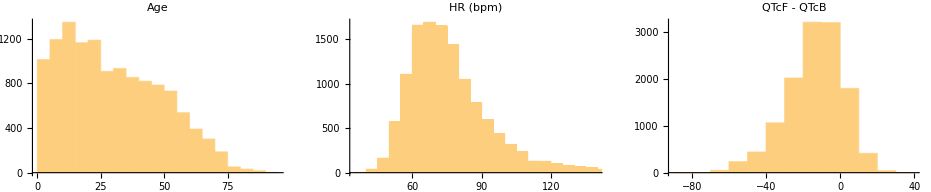

```mathematica
GraphicsRow[{
Histogram[ecgPHO[All, "Age"], PlotLabel->"Age"],
Histogram[ecgPHO[All, "HR (bpm)"], PlotLabel->"HR (bpm)"],
Histogram[fsubb, PlotLabel-> "QTcF - QTcB"]
}]
```

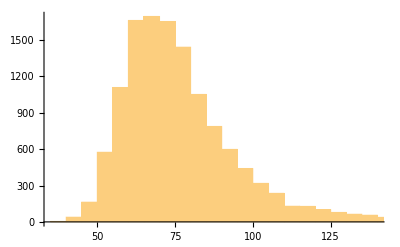

```mathematica
Histogram[ecgPHO[All, "HR (bpm)"]]
```

```mathematica
Histogram[ecgPHO[All, "QTcF (ms)"], PlotRange->{{450, Full}, {0, 600}}]
```

```mathematica
{a, b, c} - {d, e, f}
```

```mathematica
fsubb = Normal[ecgPHO[All, "QTcF (ms)"]]  - Normal[ecgPHO[All, "QTcB (ms)"]]
```

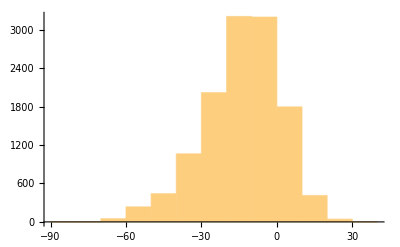

```mathematica
Histogram[fsubb]
```

```mathematica
Histogram[{fsubb, ecgPHOAge[All, "HR (bpm)"]}]
```

```mathematica
Length[fsubb]
```

```mathematica
Length[ecgPHOAge[All, "HR (bpm)"]]
```

```mathematica
hrVSfsubb = Transpose@{Normal[ecgPHOAge[All, "HR (bpm)"]], fsubb}
```

```mathematica
ages = Normal[ecgPHOAge[All, "Age"]];
```

```mathematica
age10 = Select[ages, QuantityMagnitude[#]<= 10&];
```

```mathematica
Length[age10]
```

```mathematica
ageVSfsubb = Transpose@{Normal[ecgPHO[All, "Age"]], fsubb}
```

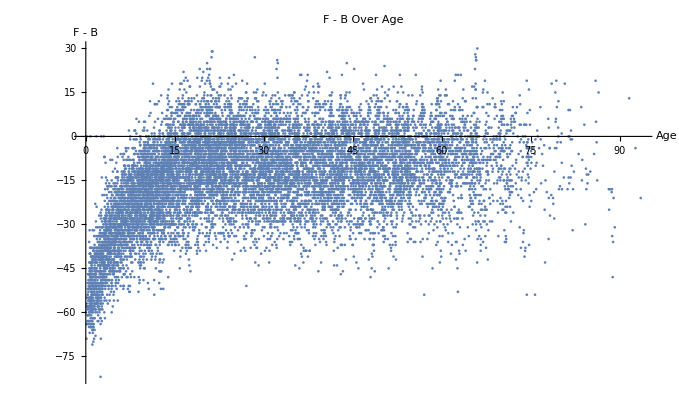

```mathematica
ListPlot[ageVSfsubb, PlotLabel->Style["F - B Over Age", Larger],AxesLabel->{Style["Age", Larger], Style["F - B", Larger]}]
```

```mathematica
age10VSfsubb = Select[ageVSfsubb, QuantityMagnitude[#[[1]]]<= 10&]
```

```mathematica
ecgPHO10yr = ecgPHO[Select[#Age<=Quantity[10, "Years"]&], {"QTcF (ms)", "QTcB (ms)"}]
```

```mathematica
ecgPHO10yr
```

```mathematica
Normal[%14]
```

```mathematica
Normal[%12]
```

```mathematica
ListPlot[{<|"a"-> 1, "b"-> 2|>, <|"a"-> 3, "b"-> 4|>}]
```

```mathematica
line1=Line[{{460,0},{460,460}}]
line2=Line[{{0, 460},{460, 460}}]
```

Line[{{460,0},{460,460}}]

Line[{{0,460},{460,460}}]

```mathematica
test2 = Labeled[Graphics[line2], "Test Cutoff"]
```

```mathematica
ListPlot[ecgPHO10yr, AxesLabel->{Style["QTcF", Large], Style["QTcB", Large]},AxesStyle->Larger, PlotRange->{{300,480}, {300, 500}}, Epilog->{line1, line2}, PlotLabel->Style["QTcB over QTcF for Kids 10 and Under", Large]]
```

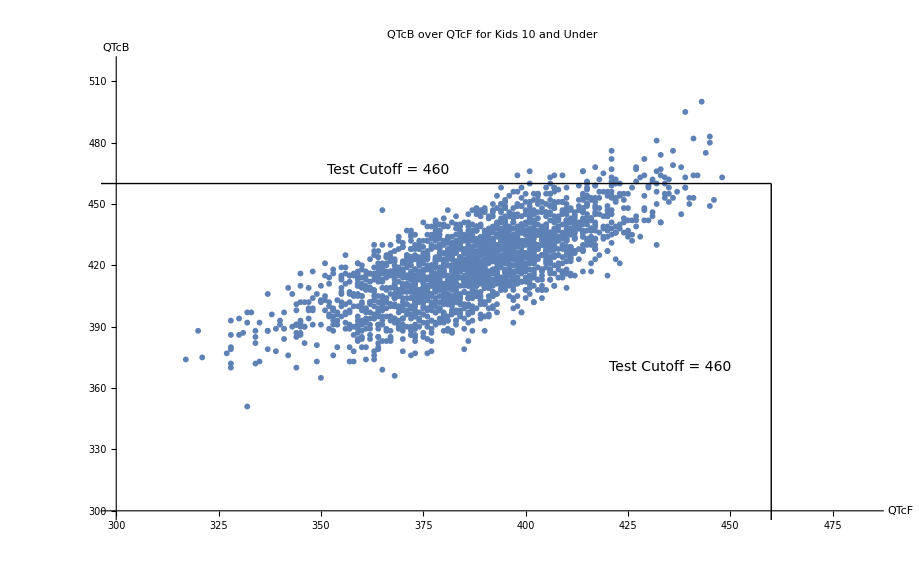

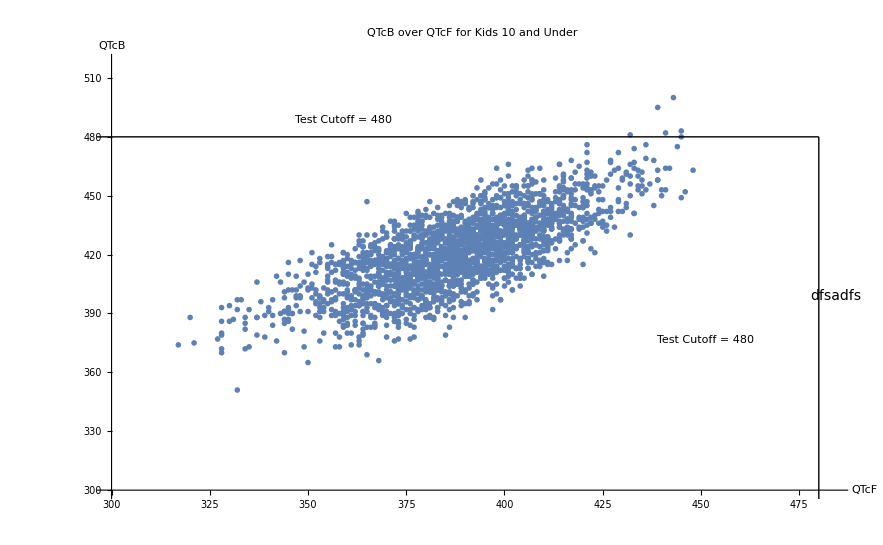

```mathematica
ListPlot[ecgPHO10yr, AxesLabel->{Style["QTcF", Large], Style["QTcB", Large]},AxesStyle->Larger, PlotRange->{{300,480}, {300, 550}}, Epilog->{line1, line2}]
```

```mathematica
ListPlot[age10VSfsubb]
```

```mathematica
Select[]
```

```mathematica
Length[hrVSfsubb]
```

```mathematica
SequenceCount[hrVSfsubb, {{52, 10}}]
```

```mathematica
ListPlot[hrVSfsubb]
```

```mathematica
fsubb[[1]]
```

```mathematica
{ecgPHOAge[All, "HR (bpm)"], ecgPHOAge[All, "Age"]}
```

```mathematica
Keys@First@ecgPHOAge
```

```mathematica
b[qt_, rr_]:= qt/Sqrt[rr]
f[qt_, rr_]:= qt/CubeRoot[rr]
qtDom = Range[380, 480, 20]
```

{380,400,420,440,460,480}

```mathematica
Plot[b[380, rr], {rr, 0.4, 1.2}]
```

```mathematica
funcs =Join[Map[Style[b[#, rr], Blue]&, qtDom], Map[Style[f[#, rr],Orange]& , qtDom]]
```

{380/(√rr),400/(√rr),420/(√rr),440/(√rr),460/(√rr),480/(√rr),380/rr^(1/3),400/rr^(1/3),420/rr^(1/3),440/rr^(1/3),460/rr^(1/3),480/rr^(1/3)}

```mathematica
Plot[{b[380, rr], b[380, rr], b[380, rr], b[440/Sqrt[rr]] ,b[460/Sqrt[rr]] ,b[480/Sqrt[rr]],
f[380/CubeRoot[rr]],f[400/CubeRoot[rr]], f[420/CubeRoot[rr]],f[440/CubeRoot[rr]],f[460/CubeRoot[rr]],f[480/CubeRoot[rr]]}, {rr, 0.4, 1.2}]
```

```mathematica
Plot[{b[qt/Sqrt[rr]], f[qt/CubeRoot[rr]]}, {rr, 0.4, 1.2}]
```

-Graphics-

```mathematica
Plot[funcs, {rr, 0.4, 1.4},PlotLabels->{380, 400, 420, 440, 460, 480}, PlotLegends->Placed[Automatic, {Right, Top}]]
```

-Graphics-